```mathematica
F[x_]:=Plus@@Times@@@FactorInteger[x]
```

```mathematica
H[x_]:=Module[{a=FixedPointList[F,x][[;;-2]],b={}},
If[Length[a]==1,Return[{a[[1]]->a[[1]]}],
For[i=1,i<Length[a],i++,
AppendTo[b,a[[i]]->a[[i+1]]]];];
Return[b]]
```

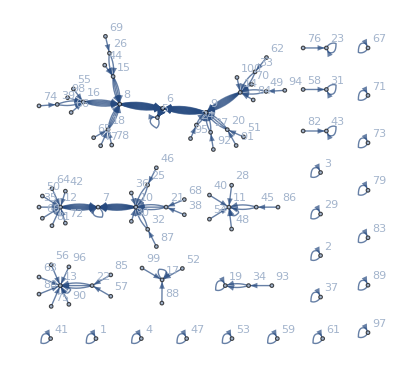

```mathematica
Graph[Flatten[Table[H[x],{x,1,100}]],VertexLabels->"Name"]
```